```mathematica
Clear["Global`*"]
κ=10;
(* World 1: B ∅ B *)
w12=g; 
w15=g;
w17=g*(1-ϵ);
w18=g*(1-ϵ)*g;
w1=1/(1+Exp[-κ*(w15+w17+w18-w12)])
```

1/(1+ⅇ^(-10 (g (1-ϵ)+g^2 (1-ϵ))))

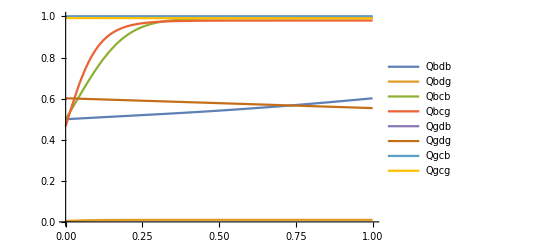

abductive_SS.pdf

```mathematica
Clear["Global`*"]
κ=10;
(* World 1: B ∅ B *)
w12=g; 
w15=g;
w17=g*(1-ϵ);
w18=g*(1-ϵ)*g;
w1=1/(1+Exp[-κ*(w15+w17+w18-w12)]);
(* World 2: B ∅ G *)
w2=0;
(* World 3: B -> B *)
w32=e*g; 
w35=g*e;
w37=g;
w38=g^2;
w3=1/(1+Exp[-κ*(w35+w37+w38-w32)]);
(* World 4: B -> G *)
w42=e; 
w45=g*e*(1-g);
w47=g*(1-g);
w48=g;
w4=1/(1+Exp[-κ*(w45+w47+w48-w42)]);
(* World 5: G ∅ B *)
w5=1;
(* World 6: G ∅ G *)
w62=1-g; 
w65=1-g;
w67=(1-ϵ)*(1-g);
w68=1-ϵ;
w6=1/(1+Exp[-κ*(w65+w67+w68-w62)]);
(* World 7: G -> G *)
w7=1;
(* World 8: G -> G *)
w8=1;
Qbdb=(1-e)*w1+e*w3;
Qbdg=(1-e)*w2+e*w4;
Qbcb=ϵ*w3+(1-ϵ)*w1;
Qbcg=ϵ*w4+(1-ϵ)*w2;
Qgdb=(1-e)*w5+e*w7;
Qgdg=(1-e)*w6+e*w8;
Qgcb=ϵ*w7+(1-ϵ)*w5;
Qgcg=ϵ*w8+(1-ϵ)*w6;
Plot[Evaluate[{Qbdb,Qbdg,Qbcb,Qbcg,Qgdb,Qgdg,Qgcb,Qgcg}/.{ϵ->0.9802,e->0.01}],{g,0,1},PlotLegends->{"Qbdb","Qbdg","Qbcb","Qbcg","Qgdb","Qgdg","Qgcb","Qgcg"}]
Export["abductive_SS.pdf",%]
```

Simple Standing

-Graphics-

abductive_SS.pdf

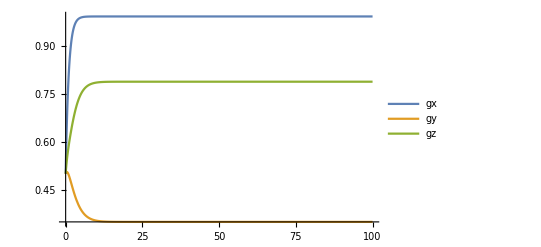

```mathematica
Simple Standing
Clear["Global`*"]
κ=10;
(* World 1: B ∅ B *)
w12=g; 
w15=g;
w17=g*(1-ϵ);
w18=g*(1-ϵ)*g;
w1=1/(1+Exp[-κ*(w15+w17+w18-w12)]);
(* World 2: B ∅ G *)
w2=0;
(* World 3: B -> B *)
w32=e*g; 
w35=g*e;
w37=g;
w38=g^2;
w3=1/(1+Exp[-κ*(w35+w37+w38-w32)]);
(* World 4: B -> G *)
w42=e; 
w45=g*e*(1-g);
w47=g*(1-g);
w48=g;
w4=1/(1+Exp[-κ*(w45+w47+w48-w42)]);
(* World 5: G ∅ B *)
w5=1;
(* World 6: G ∅ G *)
w62=1-g; 
w65=1-g;
w67=(1-ϵ)*(1-g);
w68=1-ϵ;
w6=1/(1+Exp[-κ*(w65+w67+w68-w62)]);
(* World 7: G -> G *)
w7=1;
(* World 8: G -> G *)
w8=1;
Qbdb=(1-e)*w1+e*w3;
Qbdg=(1-e)*w2+e*w4;
Qbcb=ϵ*w3+(1-ϵ)*w1;
Qbcg=ϵ*w4+(1-ϵ)*w2;
Qgdb=(1-e)*w5+e*w7;
Qgdg=(1-e)*w6+e*w8;
Qgcb=ϵ*w7+(1-ϵ)*w5;
Qgcg=ϵ*w8+(1-ϵ)*w6;
Plot[Evaluate[{Qbdb,Qbdg,Qbcb,Qbcg,Qgdb,Qgdg,Qgcb,Qgcg}/.{ϵ->0.9802,e->0.01}],{g,0,1},PlotLegends->{"Qbdb","Qbdg","Qbcb","Qbcg","Qgdb","Qgdg","Qgcb","Qgcg"}]
Export["abductive_SS.pdf",%]
g=x*gx[t]+y*gy[t]+(1-x-y)*gz[t];
g2=x*gx2[t]+y*gy2[t]+(1-x-y)*gz2[t];
repsys={
gx'[t]==(Qbcg*g+Qbcb*(1-g))-(1+(Qbcg-Qgcg)*g+(Qbcb-Qgcb)*(1-g))*gx[t],
gy'[t]==(Qbdg*g+Qbdb*(1-g))-(1+(Qbdg-Qgdg)*g+(Qbdb-Qgdb)*(1-g))*gy[t],
gz'[t]==(1-gz[t])*(Qbcg*g2+(Qbcb+Qbdg)*(g-g2)+Qbdb(1-2g+g2))-gz[t]*((1-Qbcg)*g2+(2-Qbcb-Qbdg)*(g-g2)+(1-Qbdb)*(1-2*g+g2)),
gx2'[t]==gx[t]^2-gx2[t],
gy2'[t]==gy[t]^2-gy2[t],
gz2'[t]==gz[t]^2-gz2[t]
}/.{ϵ->0.9802,e->0.01};
sol=NDSolve[Join[repsys/.{x->0.3,y->0.3},{gx[0]==0.5,gy[0]==0.5,gz[0]==0.5,gx2[0]==0.25,gy2[0]==0.25,gz2[0]==0.25}],{gx,gy,gz,gx2,gy2,gz2},{t,0,100}];
Plot[Evaluate[{gx[t],gy[t],gz[t]}/.sol],{t,0,100},PlotLegends->{"gx","gy","gz"}]
```

```mathematica
Qbdb
```

(ϵ (-2+ϵ+x gx[t]+y gy[t]+(1-x-y) gz[t])-2 e (-1+x gx[t]+y gy[t]+(1-x-y) gz[t]) (-2+ϵ+x gx[t]+y gy[t]+(1-x-y) gz[t])+e^2 (-1+x gx[t]+y gy[t]+(1-x-y) gz[t]) (-3+2 (x gx[t]+y gy[t]+(1-x-y) gz[t])))/((-ϵ+2 e (-1+x gx[t]+y gy[t]+(1-x-y) gz[t])) (3-ϵ+2 e (-1+x gx[t]+y gy[t]+(1-x-y) gz[t])-2 (x gx[t]+y gy[t]+(1-x-y) gz[t])))

```mathematica
FullSimplify[Qbdb-(1-e^2/(1+2 e+x gx[t]+y gy[t]-(-1+x+y) gz[t])+(1-e)/(-3+ϵ+x (-1+ϵ) gx[t]+y (-1+ϵ) gy[t]-(-1+x+y) (-1+ϵ) gz[t]))]
```

1/2 (-1+(2 e^2)/(1+2 e+x gx[t]+y gy[t]-(-1+x+y) gz[t])+((-1+e) (-1+ϵ))/(3-2 e-ϵ+2 (-1+e) x gx[t]+2 (-1+e) y gy[t]-2 (-1+e) (-1+x+y) gz[t])+(2 (-1+e))/(-3+ϵ+x (-1+ϵ) gx[t]+y (-1+ϵ) gy[t]-(-1+x+y) (-1+ϵ) gz[t])+(e ϵ)/(2 e+ϵ-2 e (x gx[t]+y gy[t]-(-1+x+y) gz[t])))

```mathematica
Simple Standing
Clear["Global`*"]
(* World 1: B ∅ B *)
w12=(1-g)*(1-e)*g; 
w15=g*(1-e)*(1-g);
w17=g*(1-ϵ)*(1-g);
w18=g*(1-ϵ)*g;
w1=FullSimplify[(w15+w17+w18)/(w12+w15+w17+w18)];
(* World 2: B ∅ G *)
w2=0;
(* World 3: B -> B *)
w32=(1-g)*e*g; 
w35=g*e*(1-g);
w37=g*ϵ*(1-g);
w38=g*ϵ*g;
w3=Simplify[(w35+w37+w38)/(w32+w35+w37+w38)];
(* World 4: B -> G *)
w42=(1-g)*e*g; 
w45=g*e*(1-g);
w47=g*ϵ*(1-g);
w48=g*ϵ*g;
w4=Simplify[(w45+w47+w48)/(w42+w45+w47+w48)];
(* World 5: G ∅ B *)
w5=1;
(* World 6: G ∅ G *)
w62=(1-g)*(1-e)*g; 
w65=g*(1-e)*(1-g);
w67=g*(1-ϵ)*(1-g);
w68=g*(1-ϵ)*g;
w6=Simplify[(w65+w67+w68)/(w62+w65+w67+w68)];
(* World 7: G -> G *)
w7=1;
(* World 8: G -> G *)
w8=1;
Qbdb=FullSimplify[Together[(1-e)*w1+e*w3]];
Qbdg=FullSimplify[Together[(1-e)*w2+e*w4]];
Qbcb=FullSimplify[Together[ϵ*w3+(1-ϵ)*w1]];
Qbcg=FullSimplify[Together[ϵ*w4+(1-ϵ)*w2]];
Qgdb=FullSimplify[Together[(1-e)*w5+e*w7]];
Qgdg=FullSimplify[Together[(1-e)*w6+e*w8]];
Qgcb=FullSimplify[Together[ϵ*w7+(1-ϵ)*w5]];
Qgcg=FullSimplify[Together[ϵ*w8+(1-ϵ)*w6]];
```

Simple Standing

```mathematica
Solve[(Qbcg*g+Qbcb*(1-g))/(1+(Qbcg-Qgcg)*g+(Qbcb-Qgcb)*(1-g))==g,g]
```

{{g→1},{g→(10 e-6 e^2+3 ϵ-11 e ϵ+2 e^2 ϵ-2 ϵ^2+3 e ϵ^2+ϵ^3-√(-4 (4 e-2 e^2+2 ϵ-4 e ϵ) (6 e-4 e^2-6 e ϵ+2 e^2 ϵ+2 e ϵ^2)+(-10 e+6 e^2-3 ϵ+11 e ϵ-2 e^2 ϵ+2 ϵ^2-3 e ϵ^2-ϵ^3)^2))/(2 (6 e-4 e^2-6 e ϵ+2 e^2 ϵ+2 e ϵ^2))},{g→(10 e-6 e^2+3 ϵ-11 e ϵ+2 e^2 ϵ-2 ϵ^2+3 e ϵ^2+ϵ^3+√(-4 (4 e-2 e^2+2 ϵ-4 e ϵ) (6 e-4 e^2-6 e ϵ+2 e^2 ϵ+2 e ϵ^2)+(-10 e+6 e^2-3 ϵ+11 e ϵ-2 e^2 ϵ+2 ϵ^2-3 e ϵ^2-ϵ^3)^2))/(2 (6 e-4 e^2-6 e ϵ+2 e^2 ϵ+2 e ϵ^2))}}

```mathematica
g2=g^2;
e1=0.001;
e2=0.001;
r=6;
ϵ=(1-e1)*(1-e2)+e1*e2;
e=e2;
gx=(Qbcg*g+Qbcb*(1-g))/(1+(Qbcg-Qgcg)*g+(Qbcb-Qgcb)*(1-g));
gy=(Qbdg*g+Qbdb*(1-g))/(1+(Qbdg-Qgdg)*g+(Qbdb-Qgdb)*(1-g));
gz=g Qbcb-g2 Qbcb+g2 Qbcg+Qbdb-2 g Qbdb+g2 Qbdb+g Qbdg-g2 Qbdg;
NSolve[gx==g,g]
NSolve[gy==g,g]
NSolve[(1-g)*(Qbcg*g2+(Qbcb+Qbdg)*(g-g2)+Qbdb(1-2g+g2))-g*((1-Qbcg)*g2+(2-Qbcb-Qbdg)*(g-g2)+(1-Qbdb)*(1-2*g+g2))==0,g]
```

{{g→997.009},{g→1.},{g→1.}}

{{g→500.25},{g→1.},{g→0.500999}}

{{g→1.06683},{g→1.001},{g→0.940165}}

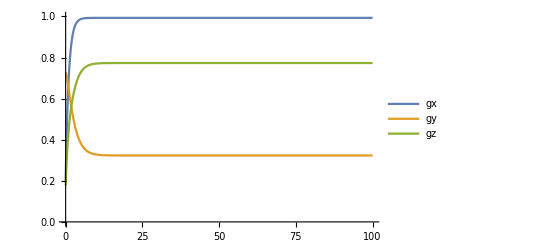

```mathematica
gx0=RandomReal[];
gy0=RandomReal[];
gz0=RandomReal[];
gx20=gx0*RandomReal[];
gy20=gy0*RandomReal[];
gz20=gz0*RandomReal[];
sol=NDSolve[Join[repsys/.{x->0.3,y->0.3},{gx[0]==gx0,gy[0]==gy0,gz[0]==gz0,gx2[0]==gx20,gy2[0]==gy20,gz2[0]==gz20}],{gx,gy,gz,gx2,gy2,gz2},{t,0,100}];
Plot[Evaluate[{gx[t],gy[t],gz[t]}/.sol],{t,0,100},PlotLegends->{"gx","gy","gz"},PlotRange->{0,1}]
```

```mathematica
Clear["Global`*"]
Solve[(1-gz)*(Qbcg*g2+(Qbcb+Qbdg)*(g-g2)+Qbdb(1-2g+g2))-gz*((1-Qbcg)*g2+(2-Qbcb-Qbdg)*(g-g2)+(1-Qbdb)*(1-2*g+g2))==0,gz]
```

{{gz→g Qbcb-g2 Qbcb+g2 Qbcg+Qbdb-2 g Qbdb+g2 Qbdb+g Qbdg-g2 Qbdg}}

Shunning

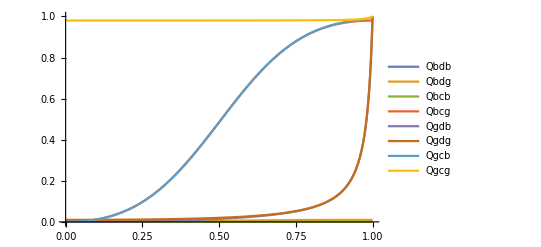

abductive_Sh.pdf

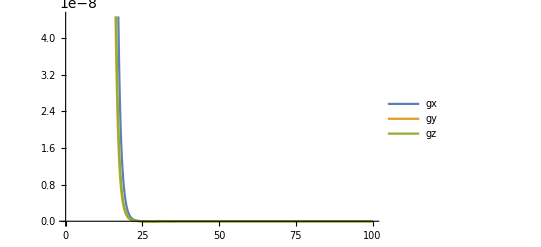

```mathematica
Shunning
Clear["Global`*"]
(* World 1: B ∅ B *)
w1=0;
(* World 2: B ∅ G *)
w2=0;
(* World 3: B -> B *)
w3=0;
(* World 4: B -> G *)
w41=(1-g)*e*(1-g); 
w42=(1-g)*e*g;
w43=(1-g)*ϵ*(1-g);
w48=g*ϵ*g;
w4=Simplify[w48/(w41+w42+w43+w48)];
(* World 5: G ∅ B *)
w51=(1-g)*(1-e)*(1-g); 
w52=(1-g)*(1-e)*g;
w53=(1-g)*(1-ϵ)*(1-g);
w58=g*(1-ϵ)*g;
w5=Simplify[w58/(w51+w52+w53+w58)];
(* World 6: G ∅ G *)
w61=(1-g)*(1-e)*(1-g); 
w62=(1-g)*(1-e)*g;
w63=(1-g)*(1-ϵ)*(1-g);
w68=g*(1-ϵ)*g;
w6=Simplify[w68/(w61+w62+w63+w68)];
(* World 7: G -> G *)
w71=(1-g)*e*(1-g); 
w72=(1-g)*e*g;
w73=(1-g)*ϵ*(1-g);
w78=g*ϵ*g;
w7=Simplify[w78/(w71+w72+w73+w78)];
(* World 8: G -> G *)
w8=1;
Qbdb=FullSimplify[Together[(1-e)*w1+e*w3]];
Qbdg=FullSimplify[Together[(1-e)*w2+e*w4]];
Qbcb=FullSimplify[Together[ϵ*w3+(1-ϵ)*w1]];
Qbcg=FullSimplify[Together[ϵ*w4+(1-ϵ)*w2]];
Qgdb=FullSimplify[Together[(1-e)*w5+e*w7]];
Qgdg=FullSimplify[Together[(1-e)*w6+e*w8]];
Qgcb=FullSimplify[Together[ϵ*w7+(1-ϵ)*w5]];
Qgcg=FullSimplify[Together[ϵ*w8+(1-ϵ)*w6]];
Plot[Evaluate[{Qbdb,Qbdg,Qbcb,Qbcg,Qgdb,Qgdg,Qgcb,Qgcg}/.{ϵ->0.9802,e->0.01}],{g,0,1},PlotLegends->{"Qbdb","Qbdg","Qbcb","Qbcg","Qgdb","Qgdg","Qgcb","Qgcg"}]
Export["abductive_Sh.pdf",%]
g=x*gx[t]+y*gy[t]+(1-x-y)*gz[t];
g2=x*gx2[t]+y*gy2[t]+(1-x-y)*gz2[t];
repsys={
gx'[t]==(Qbcg*g+Qbcb*(1-g))-(1+(Qbcg-Qgcg)*g+(Qbcb-Qgcb)*(1-g))*gx[t],
gy'[t]==(Qbdg*g+Qbdb*(1-g))-(1+(Qbdg-Qgdg)*g+(Qbdb-Qgdb)*(1-g))*gy[t],
gz'[t]==(1-gz[t])*(Qbcg*g2+(Qbcb+Qbdg)*(g-g2)+Qbdb(1-2g+g2))-gz[t]*((1-Qbcg)*g2+(2-Qbcb-Qbdg)*(g-g2)+(1-Qbdb)*(1-2*g+g2)),
gx2'[t]==gx[t]^2-gx2[t],
gy2'[t]==gy[t]^2-gy2[t],
gz2'[t]==gz[t]^2-gz2[t]
}/.{ϵ->0.9802,e->0.01};
sol=NDSolve[Join[repsys/.{x->0.3,y->0.3},{gx[0]==0.5,gy[0]==0.5,gz[0]==0.5,gx2[0]==0.25,gy2[0]==0.25,gz2[0]==0.25}],{gx,gy,gz,gx2,gy2,gz2},{t,0,100}];
Plot[Evaluate[{gx[t],gy[t],gz[t]}/.sol],{t,0,100},PlotLegends->{"gx","gy","gz"}]
```

Judging Stern

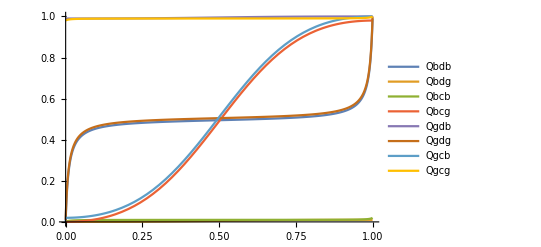

abductive_SJ.pdf

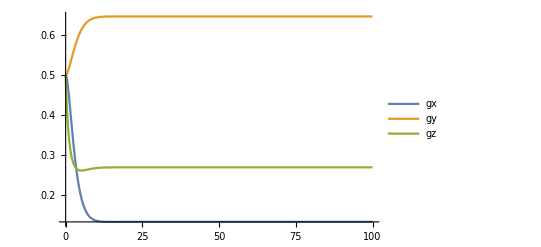

```mathematica
Stern Judging
Clear["Global`*"]
(* World 1: B ∅ B *)
w12=(1-g)*(1-e)*g; 
w13=(1-g)*(1-ϵ)*(1-g);
w15=g*(1-e)*(1-g);
w18=g*(1-ϵ)*g;
w1=Simplify[(w15+w18)/(w12+w13+w15+w18)];
(* World 2: B ∅ G *)
w2=0;
(* World 3: B -> B *)
w3=0;
(* World 4: B -> G *)
w42=(1-g)*e*g; 
w43=(1-g)*ϵ*(1-g);
w45=g*e*(1-g);
w48=g*ϵ*g;
w4=Simplify[(w45+w48)/(w42+w43+w45+w48)];
(* World 5: G ∅ B *)
w5=1;
(* World 6: G ∅ G *)
w62=(1-g)*(1-e)*g; 
w63=(1-g)*(1-ϵ)*(1-g);
w65=g*(1-e)*(1-g);
w68=g*(1-ϵ)*g;
w6=Simplify[(w65+w68)/(w62+w63+w65+w68)];
(* World 7: G -> G *)
w72=(1-g)*e*g; 
w73=(1-g)*ϵ*(1-g);
w75=g*e*(1-g);
w78=g*ϵ*g;
w7=Simplify[(w75+w78)/(w72+w73+w75+w78)];
(* World 8: G -> G *)
w8=1;
Qbdb=FullSimplify[Together[(1-e)*w1+e*w3]];
Qbdg=FullSimplify[Together[(1-e)*w2+e*w4]];
Qbcb=FullSimplify[Together[ϵ*w3+(1-ϵ)*w1]];
Qbcg=FullSimplify[Together[ϵ*w4+(1-ϵ)*w2]];
Qgdb=FullSimplify[Together[(1-e)*w5+e*w7]];
Qgdg=FullSimplify[Together[(1-e)*w6+e*w8]];
Qgcb=FullSimplify[Together[ϵ*w7+(1-ϵ)*w5]];
Qgcg=FullSimplify[Together[ϵ*w8+(1-ϵ)*w6]];
Plot[Evaluate[{Qbdb,Qbdg,Qbcb,Qbcg,Qgdb,Qgdg,Qgcb,Qgcg}/.{ϵ->0.9802,e->0.01}],{g,0,1},PlotLegends->{"Qbdb","Qbdg","Qbcb","Qbcg","Qgdb","Qgdg","Qgcb","Qgcg"}]
Export["abductive_SJ.pdf",%]
g=x*gx[t]+y*gy[t]+(1-x-y)*gz[t];
g2=x*gx2[t]+y*gy2[t]+(1-x-y)*gz2[t];
repsys={
gx'[t]==(Qbcg*g+Qbcb*(1-g))-(1+(Qbcg-Qgcg)*g+(Qbcb-Qgcb)*(1-g))*gx[t],
gy'[t]==(Qbdg*g+Qbdb*(1-g))-(1+(Qbdg-Qgdg)*g+(Qbdb-Qgdb)*(1-g))*gy[t],
gz'[t]==(1-gz[t])*(Qbcg*g2+(Qbcb+Qbdg)*(g-g2)+Qbdb(1-2g+g2))-gz[t]*((1-Qbcg)*g2+(2-Qbcb-Qbdg)*(g-g2)+(1-Qbdb)*(1-2*g+g2)),
gx2'[t]==gx[t]^2-gx2[t],
gy2'[t]==gy[t]^2-gy2[t],
gz2'[t]==gz[t]^2-gz2[t]
}/.{ϵ->0.9802,e->0.01};
sol=NDSolve[Join[repsys/.{x->0.3,y->0.3},{gx[0]==0.5,gy[0]==0.5,gz[0]==0.5,gx2[0]==0.25,gy2[0]==0.25,gz2[0]==0.25}],{gx,gy,gz,gx2,gy2,gz2},{t,0,100}];
Plot[Evaluate[{gx[t],gy[t],gz[t]}/.sol],{t,0,100},PlotLegends->{"gx","gy","gz"}]
```

Scoring

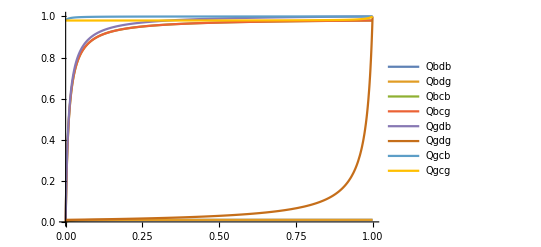

abductive_Sc.pdf

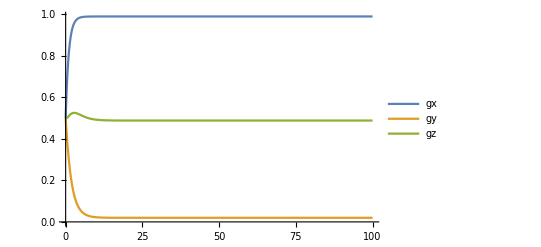

```mathematica
Scoring
Clear["Global`*"]
(* World 1: B ∅ B *)
w1=0;
(* World 2: B ∅ G *)
w2=0;
(* World 3: B -> B *)
w31=(1-g)*e*g; 
w32=(1-g)*e*(1-g);
w37=g*ϵ*(1-g);
w38=g*ϵ*g;
w3=Simplify[(w37+w38)/(w31+w32+w37+w38)];
(* World 4: B -> G *)
w41=(1-g)*e*g; 
w42=(1-g)*e*(1-g);
w47=g*ϵ*(1-g);
w48=g*ϵ*g;
w4=Simplify[(w47+w48)/(w41+w42+w47+w48)];
(* World 5: G ∅ B *)
w51=(1-g)*(1-e)*g; 
w52=(1-g)*(1-e)*(1-g);
w57=g*ϵ*(1-g);
w58=g*ϵ*g;
w5=Simplify[(w47+w48)/(w41+w42+w47+w48)];
(* World 6: G ∅ G *)
w61=(1-g)*(1-e)*g; 
w62=(1-g)*(1-e)*(1-g);
w67=g*(1-ϵ)*(1-g);
w68=g*(1-ϵ)*g;
w6=Simplify[(w67+w68)/(w61+w62+w67+w68)];
(* World 7: G -> G *)
w7=1;
(* World 8: G -> G *)
w8=1;
Qbdb=FullSimplify[Together[(1-e)*w1+e*w3]];
Qbdg=FullSimplify[Together[(1-e)*w2+e*w4]];
Qbcb=FullSimplify[Together[ϵ*w3+(1-ϵ)*w1]];
Qbcg=FullSimplify[Together[ϵ*w4+(1-ϵ)*w2]];
Qgdb=FullSimplify[Together[(1-e)*w5+e*w7]];
Qgdg=FullSimplify[Together[(1-e)*w6+e*w8]];
Qgcb=FullSimplify[Together[ϵ*w7+(1-ϵ)*w5]];
Qgcg=FullSimplify[Together[ϵ*w8+(1-ϵ)*w6]];
Plot[Evaluate[{Qbdb,Qbdg,Qbcb,Qbcg,Qgdb,Qgdg,Qgcb,Qgcg}/.{ϵ->0.9802,e->0.01}],{g,0,1},PlotLegends->{"Qbdb","Qbdg","Qbcb","Qbcg","Qgdb","Qgdg","Qgcb","Qgcg"}]
Export["abductive_Sc.pdf",%]
g=x*gx[t]+y*gy[t]+(1-x-y)*gz[t];
g2=x*gx2[t]+y*gy2[t]+(1-x-y)*gz2[t];
repsys={
gx'[t]==(Qbcg*g+Qbcb*(1-g))-(1+(Qbcg-Qgcg)*g+(Qbcb-Qgcb)*(1-g))*gx[t],
gy'[t]==(Qbdg*g+Qbdb*(1-g))-(1+(Qbdg-Qgdg)*g+(Qbdb-Qgdb)*(1-g))*gy[t],
gz'[t]==(1-gz[t])*(Qbcg*g2+(Qbcb+Qbdg)*(g-g2)+Qbdb(1-2g+g2))-gz[t]*((1-Qbcg)*g2+(2-Qbcb-Qbdg)*(g-g2)+(1-Qbdb)*(1-2*g+g2)),
gx2'[t]==gx[t]^2-gx2[t],
gy2'[t]==gy[t]^2-gy2[t],
gz2'[t]==gz[t]^2-gz2[t]
}/.{ϵ->0.9802,e->0.01};
sol=NDSolve[Join[repsys/.{x->0.3,y->0.3},{gx[0]==0.5,gy[0]==0.5,gz[0]==0.5,gx2[0]==0.25,gy2[0]==0.25,gz2[0]==0.25}],{gx,gy,gz,gx2,gy2,gz2},{t,0,100}];
Plot[Evaluate[{gx[t],gy[t],gz[t]}/.sol],{t,0,100},PlotLegends->{"gx","gy","gz"}]
```